## Study the optimized modulating parameter

```mathematica
Clear["Global`*"];
```

```mathematica
SetDirectory[NotebookDirectory[]];
transPars=Import["saturationSamplingOptimizingTModulating1E4.csv"];
```

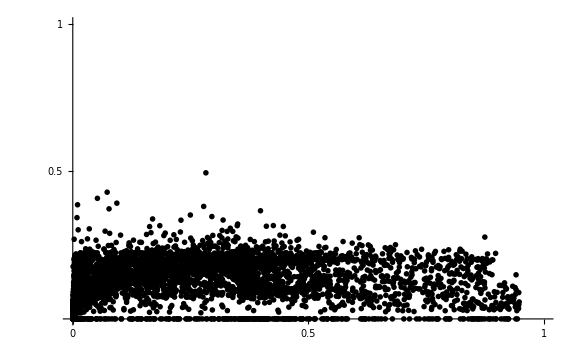

```mathematica
ListPlot[Transpose[{transPars[[15]],transPars[[16]]}],PlotRange->{{0,1},{0,1}},(*AxesLabel->{"Ultrasensitive score","Adaptive score"},*)Ticks->{{0,0.5,1}, {0.5,1}},PlotStyle->{Thick,PointSize[0.01]},PlotTheme->"Monochrome",PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large]
```

```mathematica
us20index=Reverse[Ordering[transPars[[15]],-20]]
```

{9517,8328,7420,2119,2203,9491,8652,8303,6284,9455,4421,5117,7295,5016,474,1185,6146,9970,4192,2565}

```mathematica
ad20index=Reverse[Ordering[transPars[[16]],-20]]
```

{554,942,2559,3487,3400,5898,9465,3885,7089,6696,5293,4562,7342,9524,3999,6549,1266,1944,1421,6073}

```mathematica
ad10index=Reverse[Ordering[transPars[[16]],-20]]
```

{554,942,2559,3487,3400,5898,9465,3885,7089,6696,5293,4562,7342,9524,3999,6549,1266,1944,1421,6073}

```mathematica
adUs20index=Reverse[Ordering[(Sqrt[transPars[[16]]]*(transPars[[15]])^8),-20]]
```

{6284,6402,7295,8303,7420,4192,3038,147,4421,5786,8025,4187,4814,2217,527,3482,2118,7769,5970,8275}

```mathematica
pars=Transpose[transPars];
```

```mathematica
ad10pars=pars[[ad10index]];
```

```mathematica
(*Clear["Global`*"];*)
SetDirectory[NotebookDirectory[]];
kd=10;
des={-k[1]* x[1][t] *x[3][t]+k[2]* x[5][t]+k[3] *x[5][t]-k[7]* x[1][t]* x[7][t]+k[8]*x[8][t]+k11[t]*kd-kd*x[1][t],-k[4]* x[2][t] *x[4][t]+k[5]* x[6][t]+k[6] *x[6][t]-k[9]* x[2][t]* x[7][t]+k[10]* x[9][t],-k[1]* x[1][t] *x[3][t]+k[2] *x[5][t]+k[6]*x[6][t],
-k[4]*x[2][t]* x[4][t]+k[3]*x[5][t]+k[5]* x[6][t],
k[1]* x[1][t] *x[3][t]-k[2] *x[5][t]-k[3]* x[5][t],
k[4] *x[2][t]* x[4][t]-k[5] *x[6][t]-k[6] *x[6][t],-k[7] *x[1][t]* x[7][t]-k[9] *x[2][t]* x[7][t]+k[8]* x[8][t]+k[10]*x[9][t],
k[7]* x[1][t] *x[7][t]-k[8]* x[8][t],
k[9] *x[2][t] *x[7][t]-k[10] *x[9][t],0};

init={totK,totP,totS,0,0,0,totT,0,0,1.*10^-4};(*init={tot[1],tot[2],tot[3],0.00001,0.00001,0.00001,totT,0.00001,0.00001};*)

colorf=Blend[{{Min[altitude],Cyan},{Max[altitude],Magenta}},#]&;
plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->False,FrameTicks->None,PlotRangePadding->.5];
```

Now, we re-sample the [T] to get the new drawings but with colour as [T]

```mathematica
AbsoluteTiming[

SetDirectory[NotebookDirectory[]];
vars=Array[x,9];AppendTo[vars,k11];
dvars=Thread[Derivative[1][vars]];
SeedRandom[];
ts={};
Block[{points,iPar,num,adToUsPars,maxPars,transPars},
totK=0.0001;totP=0.1;totS=1;
stepNum=5;
sampleSize=1000;
points=20;

For[iPar=1,iPar≤points,iPar++,
maxPars=Solve[Array[k,10]==ad10pars[[iPar]][[Range[10]]]];
adToUsPars={};

For[num=1,num≤sampleSize,num++,
Block[{ssthreshold},
(*tot[n_]:=tot[n]=10^(RandomReal[]*4-3);*)
(*ksTest1=Array[k,10];*)
(*totT=1.*^-3;*)
totT=1.*10^(RandomReal[]*6-3);

Block[{tPer,step,us,ad,x4,sol},
step=0;
tPer={};
ssthreshold=1.*^-5;
(* Print[des]; *){sol}=NDSolve[{Through[dvars[t]]==des,Through[vars[0]]==init,With[{df=Through[dvars[t]]},WhenEvent[Norm[df]<ssthreshold,{AppendTo[tPer,t],step=step+1,If[step>stepNum,"StopIntegration"],k11[t]->10*k11[t]}]]}/.maxPars,vars,{t,0,200000},MaxSteps->10000];
ts=tPer;
If[Length[ts]==stepNum+1 &&AllTrue[ts,Positive],
x4=Evaluate[x[4][ts-0.001]/.sol];xT=Evaluate[(x[7][ts-0.001]+x[8][ts-0.001]+x[9][ts-0.001])/.sol];

us=Sqrt[((Abs[(x4[[4]]-x4[[3]])]/totS)*Min[((Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[3]]-x4[[1]])],0.001]+Abs[(x4[[4]]-x4[[3]])]/Max[Abs[(x4[[stepNum+1]]-x4[[4]])],0.001])/2)/10.0,1.0])];

ad=0.0001;
For[i=1,i≤stepNum,i++,
ad=ad*Sqrt[(Min[(Max[Abs[Evaluate[x[4][Range[ts[[i]],ts[[i+1]],1]]/.sol]-Evaluate[x[4][ts[[i]]]/.sol]]]/(0.2*totS)),1.0]*((0.01)/(Max[Abs[(x4[[i+1]]-x4[[i]])/totS],0.01])))];
];
ad=(ad/0.0001)^(1/(stepNum));

AppendTo[adToUsPars,{totT,us,ad,num}];
];
];
];
];
transAdToUsPars=Transpose[adToUsPars];

usVsAd=Transpose[{transAdToUsPars[[2]],transAdToUsPars[[3]]}];
altitude= Log10[transAdToUsPars[[1]]];
colorf=Blend[{{Min[altitude],Cyan},{Max[altitude],Magenta}},#]&;
plotLegend[{min_,max_},n_,col_]:=Graphics[MapIndexed[{{col[#1],Rectangle[{0,#2[[1]]-1},{1,#2[[1]]}]},{Black,Text[NumberForm[N@#1,{4,2}],{4,#2[[1]]-.5},{1,0}]}}&,Rescale[Range[n],{1,n},{min,max}]],Frame->False,FrameTicks->None,PlotRangePadding->.5];

vsPlot=Graphics[MapThread[{colorf[#1],{PointSize[Large],Point[#2]}}&,{altitude,usVsAd}],Axes->True,AspectRatio->1,PlotRange->{{0,1},{0,1}},Ticks->{{0,0.5,1}, {0.5,1}},PlotLabel->None,LabelStyle->{24,GrayLevel[0]},ImageSize->Large];
(*Export[NotebookDirectory[]<>"saturatedAdToUsColour"<>ToString[iPar]<>".pdf",vsPlot];
Export[NotebookDirectory[]<>"saturatedAdToUsColour"<>ToString[iPar]<>".eps",vsPlot];*)
leg=plotLegend[Through[{Min,Max}[altitude]],9,colorf];
legTxt=Graphics[Text[StyleForm["Log_10([T])",FontSize->14,FontWeight->"Bold"]]];
pLeg=Grid[{{Show[vsPlot,ImageSize->{Automatic,600}],Grid[{{Show[legTxt,ImageSize->{100,50}]},{Show[leg,ImageSize->{100,Automatic}]}}]}}];
Export[NotebookDirectory[]<>"saturatedModulationOptimizedAdToUsColourLeg"<>ToString[iPar]<>".pdf",pLeg];
Export[NotebookDirectory[]<>"saturatedModulationOptimizedAdToUsColourLeg"<>ToString[iPar]<>".eps",pLeg];

];
];
]
```

{4642.38,Null}